```mathematica
hmatrix={{h11,h12},{h12,-h11}};
%//MatrixForm
rho = {{r11,a+I b},{a-I b,r22}};
%//MatrixForm
```

(h11 | h12
h12 | -h11)

(r11 | a+ⅈ b
a-ⅈ b | r22)

```mathematica
hmatrix.rho -rho.hmatrix//FullSimplify
%//MatrixForm
```

{{-2 ⅈ b h12,2 a h11+2 ⅈ b h11+h12 (-r11+r22)},{-2 a h11+2 ⅈ b h11+h12 (r11-r22),2 ⅈ b h12}}

(-2 ⅈ b h12 | 2 a h11+2 ⅈ b h11+h12 (-r11+r22)
-2 a h11+2 ⅈ b h11+h12 (r11-r22) | 2 ⅈ b h12)

In the case of 
h21=h12,
h12+h21=2h12,
h11+h22=0,
h11-h22=2h11.

I am going to define a list which is

```mathematica
commutator = {-2 b h12,2 a h11+h12 (-r11+r22),2 b h11,2  b h12}
```

{-2 b h12,2 a h11+h12 (-r11+r22),2 b h11,2 b h12}

### Another Approach

```mathematica
hmatrix4={{h0,h1},{h2,h3}}
%//MatrixForm
```

{{h0,h1},{h2,h3}}

(h0 | h1
h2 | h3)

```mathematica
rho4={{r0,r2+I r3},{r2-I r3,r1}}
rhop4={{rp0,rp2+I rp3},{rp2-I rp3,rp1}}
```

{{r0,r2+ⅈ r3},{r2-ⅈ r3,r1}}

{{rp0,rp2+ⅈ rp3},{rp2-ⅈ rp3,rp1}}

```mathematica
commutator4=hmatrix4.rho4 -rho4.hmatrix4//FullSimplify
%//MatrixForm
```

{{(h1-h2) r2-ⅈ (h1+h2) r3,h1 (-r0+r1)+(h0-h3) (r2+ⅈ r3)},{h2 (r0-r1)-(h0-h3) (r2-ⅈ r3),(-h1+h2) r2+ⅈ (h1+h2) r3}}

((h1-h2) r2-ⅈ (h1+h2) r3 | h1 (-r0+r1)+(h0-h3) (r2+ⅈ r3)
h2 (r0-r1)-(h0-h3) (r2-ⅈ r3) | (-h1+h2) r2+ⅈ (h1+h2) r3)

```mathematica
Table[I rhop4[[i,j]]==commutator4[[i,j]],{i,1,2},{j,1,2}]
%//FullSimplify
%//MatrixForm
```

{{ⅈ rp0==(h1-h2) r2-ⅈ (h1+h2) r3,ⅈ (rp2+ⅈ rp3)==h1 (-r0+r1)+(h0-h3) (r2+ⅈ r3)},{ⅈ (rp2-ⅈ rp3)==h2 (r0-r1)-(h0-h3) (r2-ⅈ r3),ⅈ rp1==(-h1+h2) r2+ⅈ (h1+h2) r3}}

{{ⅈ rp0==(h1-h2) r2-ⅈ (h1+h2) r3,ⅈ rp2==h1 (-r0+r1)+(h0-h3) (r2+ⅈ r3)+rp3},{(h0-h3) (r2-ⅈ r3)+ⅈ rp2+rp3==h2 (r0-r1),ⅈ rp1==(-h1+h2) r2+ⅈ (h1+h2) r3}}

(ⅈ rp0==(h1-h2) r2-ⅈ (h1+h2) r3 | ⅈ rp2==h1 (-r0+r1)+(h0-h3) (r2+ⅈ r3)+rp3
(h0-h3) (r2-ⅈ r3)+ⅈ rp2+rp3==h2 (r0-r1) | ⅈ rp1==(-h1+h2) r2+ⅈ (h1+h2) r3)

### Plots

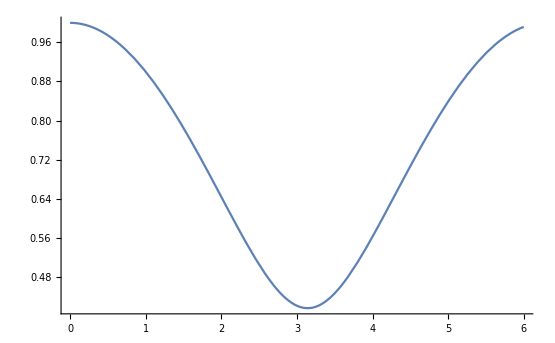

```mathematica
Plot[Sqrt[1-Sin[2]^2 Sin[0.5 x]^2],{x,0,6}]
```